```mathematica
P[x_,y_]:=-I*η+ξ^2
```

```mathematica
Int[a_,b_]:=Integrate[E^(-I*P[η,ξ]),{η,-a,a},{ξ,-b,b}]
```

```mathematica
Int[a,b]
```

-2 (-1)^(3/4) √π Erf[(-1)^(1/4) b] Sinh[a]

```mathematica
FF[a_]:=Integrate[E^(-I*I*x),{x,-a,a}]
```

```mathematica
N[Limit[FF[a],a-> 100]]
```

2.68812×10^43

```mathematica
Integrate[E^(-I*x^2),{x,-Infinity,Infinity}]
```

(1-ⅈ) √(π/2)

```mathematica
N[Sinh[100]-Sinh[-100]]
```

2.68812×10^43

```mathematica
N[Erf[-100]]
```

-1.

```mathematica
Integrate[(t^T)*E^(-I*t^(4)),{t,0,A}]
```

ConditionalExpression[A^(1+T) (HypergeometricPFQ[{1/8+T/8},{1/2,9/8+T/8},-A^8/4]/(1+T)-(ⅈ √(A^8) HypergeometricPFQ[{5/8+T/8},{3/2,13/8+T/8},-A^8/4])/(5+T)),Re[T]>-1&&Re[A]≥0]

```mathematica
Integrate[E^(-I*(x^2+y^2)),{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

-ⅈ π

```mathematica
(2*Pi^(2/2))/Gamma[2/2]*Integrate[E^(-I*r),{r,0,Infinity}]
```

Integrate::idiv: Integral of ⅇ^-ⅈ\ r does not converge on {0, ∞}.

2 π ∫_0^∞ ⅇ^(-ⅈ r)ⅆr

```mathematica
-ⅈ ⅇ^(-1/2 ⅈ π T) Gamma[1+T]//TeXForm
```

-i e^{-\frac{1}{2} i \pi  T} \Gamma (T+1)

```mathematica
-ⅈ ⅇ^(-1/2 ⅈ π T) Gamma[1+T]//TeXForm
```

-i e^{-\frac{1}{2} i \pi  T} \Gamma (T+1)

```mathematica
Λ={(d2*d3)*t^(1/d1)*Sin[θ]*Cos[ϕ],(d1*d3)*t^(1/d2)*Sin[θ]*Sin[ϕ],(d1*d2)t^(1/d3)*Cos[θ]}
```

{d2 d3 t^(1/d1) Cos[ϕ] Sin[θ],d1 d3 t^(1/d2) Sin[θ] Sin[ϕ],d1 d2 t^(1/d3) Cos[θ]}

```mathematica
S={t^(1/d1)*Cos[θ],t^(1/d2)*Sin[θ]}
```

{t^(1/d1) Cos[θ],t^(1/d2) Sin[θ]}

```mathematica
GenS={t^(1/d1)*Cos[θ]^(2/d1),t^(1/d2)*Sin[θ]^(2/d2)}
```

{t^(1/d1) Cos[θ]^(2/d1),t^(1/d2) Sin[θ]^(2/d2)}

```mathematica
CdS = {t,θ}
```

{t,θ}

```mathematica
Cd={t,θ,ϕ}
```

{t,θ,ϕ}

```mathematica
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})

JacobianDeterminant[f_List?VectorQ,x_List]:=Det[JacobianMatrix[f,x]]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
JS = JacobianMatrix[S,CdS]
```

{{(t^(-1+1/d1) Cos[θ])/d1,-t^(1/d1) Sin[θ]},{(t^(-1+1/d2) Sin[θ])/d2,t^(1/d2) Cos[θ]}}

```mathematica
JS//MatrixForm
```

((t^(-1+1/d1) Cos[θ])/d1 | -t^(1/d1) Sin[θ]
(t^(-1+1/d2) Sin[θ])/d2 | t^(1/d2) Cos[θ])

```mathematica
JS//MatrixForm
```

((t^(-1+1/d1) Cos[θ]^(2/d1))/d1 | -(2 t^(1/d1) Cos[θ]^(-1+2/d1) Sin[θ])/d1
(t^(-1+1/d2) Sin[θ]^(2/d2))/d2 | (2 t^(1/d2) Cos[θ] Sin[θ]^(-1+2/d2))/d2)

```mathematica
Det[JS]//Simplify
```

(2 t^(-1+1/d1+1/d2) Cos[θ]^(-1+2/d1) Sin[θ]^(-1+2/d2))/(d1 d2)

```mathematica
JacobianDeterminant[JS,CdS]
```

JacobianDeterminant[{{(t^(-1+1/d1) Cos[θ]^(2/d1))/d1,-(2 t^(1/d1) Cos[θ]^(-1+2/d1) Sin[θ])/d1},{(t^(-1+1/d2) Sin[θ]^(2/d2))/d2,(2 t^(1/d2) Cos[θ] Sin[θ]^(-1+2/d2))/d2}},{t,θ}]

```mathematica
J =JacobianMatrix[Λ,Cd]//MatrixForm
```

((d2 d3 t^(-1+1/d1) Cos[ϕ] Sin[θ])/d1 | d2 d3 t^(1/d1) Cos[θ] Cos[ϕ] | -d2 d3 t^(1/d1) Sin[θ] Sin[ϕ]
(d1 d3 t^(-1+1/d2) Sin[θ] Sin[ϕ])/d2 | d1 d3 t^(1/d2) Cos[θ] Sin[ϕ] | d1 d3 t^(1/d2) Cos[ϕ] Sin[θ]
(d1 d2 t^(-1+1/d3) Cos[θ])/d3 | -d1 d2 t^(1/d3) Sin[θ] | 0)

```mathematica
J//MatrixForm
```

((d2 d3 t^(-1+1/d1) Cos[ϕ] Sin[θ])/d1 | d2 d3 t^(1/d1) Cos[θ] Cos[ϕ] | -d2 d3 t^(1/d1) Sin[θ] Sin[ϕ]
(d1 d3 t^(-1+1/d2) Sin[θ] Sin[ϕ])/d2 | d1 d3 t^(1/d2) Cos[θ] Sin[ϕ] | d1 d3 t^(1/d2) Cos[ϕ] Sin[θ]
(d1 d2 t^(-1+1/d3) Cos[θ])/d3 | -d1 d2 t^(1/d3) Sin[θ] | 0)

```mathematica
JacobianDeterminant[Λ,Cd]//Simplify
```

d1 d2 d3 t^(-1+1/d1+1/d2+1/d3) Sin[θ] (d1 d2 Cos[θ]^2+d3 Sin[θ]^2 (d2 Cos[ϕ]^2+d1 Sin[ϕ]^2))

```mathematica
Integrate[(1/2)*Cos[t]^2 + (1/4)*Sin[t]^2,{t,0,2Pi}]
```

(3 π)/4

```mathematica
(1/16)*Integrate[t^(-1+2/4)*E^(I*t*(Cos[th]^4+Sin[th]^4)),{t,0,Infinity},{th,0,2Pi}]
```

(2+2 ⅈ) √(2 π) EllipticK[1/2]

```mathematica
Integrate[t^(-1+2/6)*E^(I*t*(Cos[th]^6+Sin[th]^6)),{t,0,Infinity},{th,0,2Pi}]
```

(2 π^2 Hypergeometric2F1[1/6,2/3,1,9/25] Root[110592+25 #1^6&,1])/Gamma[-1/3]

```mathematica
Integrate[t^(-1+2/8)*E^(I*t*(Cos[th]^8+Sin[th]^8)),{t,0,Infinity},{th,0,2Pi}]
```

32 (-1)^(1/8) Gamma[9/8]^2

```mathematica
Integrate[t^(-1+2/10)*E^(I*t*(Cos[th]^10+Sin[th]^10)),{t,0,Infinity},{th,0,2Pi}]
```

$Aborted

```mathematica
N[EllipticK[1/2]]
```

1.85407

```mathematica
N[Root[110592+25 #1^6&,1]]
```

-3.50882-2.02582 ⅈ

```mathematica
Integrate[E^(I*t),{t,0,Infinity}]
```

Integrate::idiv: Integral of ⅇ^ⅈ\ t does not converge on {0, ∞}.

∫_0^∞ ⅇ^(ⅈ t)ⅆt

```mathematica
Integrate[Cos[t],{t,0,Infinity}]
```

Integrate::idiv: Integral of InterpretationBox[StyleBox[Cos, Rule[AutoSpacing, False], Rule[ShowAutoStyles, False]], Cos, Rule[Editable, False]] does not converge on {0, ∞}.

∫_0^∞ Cos[t]ⅆt

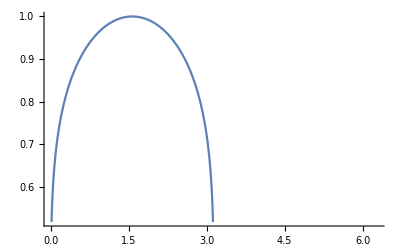

```mathematica
Plot[Sin[t]^(1/6),{t,0,2Pi}]
```

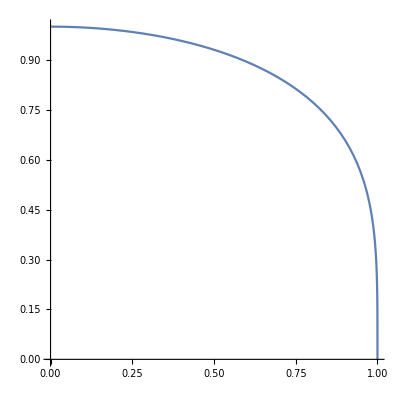

```mathematica
P1=ParametricPlot[{Sin[2t],Sqrt[Cos[2t]]},{t,0,Pi/4}]
```

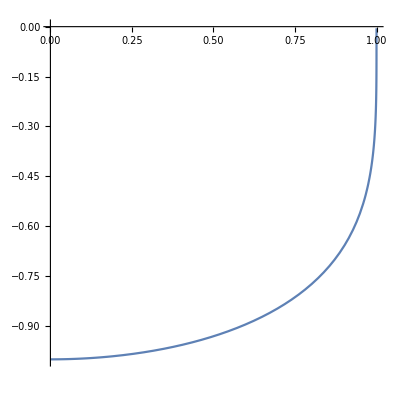

```mathematica
P2=ParametricPlot[{Sin[2t],-Sqrt[-Cos[2t]]},{t,Pi/4,Pi/2}]
```

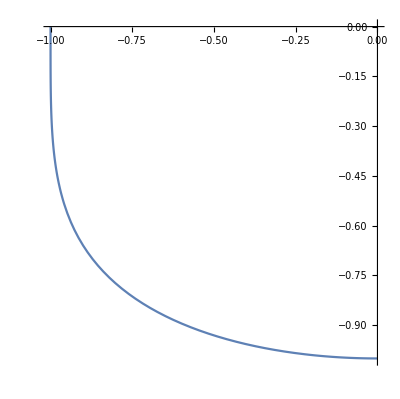

```mathematica
P3=ParametricPlot[{Sin[2t],-Sqrt[-Cos[2t]]},{t,Pi/2,3Pi/4}]
```

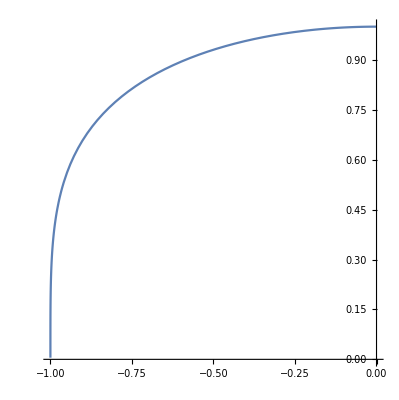

```mathematica
P4=ParametricPlot[{Sin[2t],Sqrt[Cos[2t]]},{t,3Pi/4,Pi}]
```

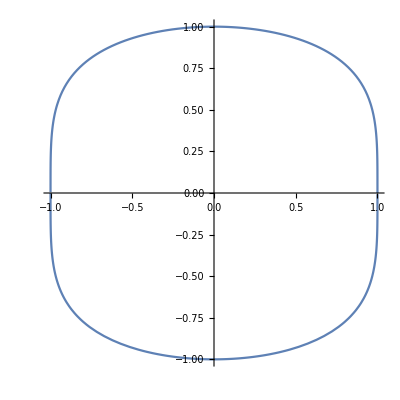

```mathematica
Show[ParametricPlot[{Sin[2t],Sqrt[Cos[2t]]},{t,0,Pi/4}],
ParametricPlot[{Sin[2t],-Sqrt[-Cos[2t]]},{t,Pi/4,3Pi/4}],
ParametricPlot[{Sin[2t],Sqrt[Cos[2t]]},{t,3Pi/4,Pi}],PlotRange-> {-1,1}]
```

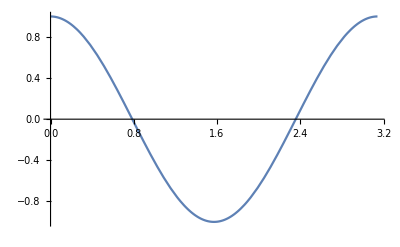

```mathematica
Plot[Cos[2t],{t,0,Pi}]
```

```mathematica
Sqrt[Cos[Pi]]
```

ⅈ

```mathematica
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})

JacobianDeterminant[f_List?VectorQ,x_List]:=Det[JacobianMatrix[f,x]]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
S={t^(1/2)*Sin[2θ],t^(1/4)*Sqrt[Cos[2θ]]}
```

{√t Sin[2 θ],t^(1/4) √Cos[2 θ]}

```mathematica
CdS= {t,θ}
```

{t,θ}

```mathematica
JacobianDeterminant[S,CdS]//Simplify
```

-1/(2 t^(1/4) √Cos[2 θ])

```mathematica
Integrate[-1/(2 t^(1/4) √Cos[2 θ]),{θ,0,Pi/4}]
```

-EllipticK[1/2]/(2 √2 t^(1/4))

```mathematica
Transpose[JacobianMatrix[S,CdS]].JacobianMatrix[S,CdS]
```

{{Cos[2 θ]/(16 t^(3/2))+Sin[2 θ]^2/(4 t),-Sin[2 θ]/(4 √t)+Cos[2 θ] Sin[2 θ]},{-Sin[2 θ]/(4 √t)+Cos[2 θ] Sin[2 θ],4 t Cos[2 θ]^2+√t Sin[2 θ] Tan[2 θ]}}

```mathematica
Det[JacobianMatrix[S,CdS].Transpose[JacobianMatrix[S,CdS]]]//Simplify
```

Sec[2 θ]/(4 √t)

```mathematica
Integrate[Sec[2 θ]/(4 √t),{θ,0,Pi/4}]
```

Integrate::idiv: Integral of Sec[2\ θ] does not converge on {0, π/4}.

∫_0^(π/4) Sec[2 θ]/(4 √t)ⅆθ

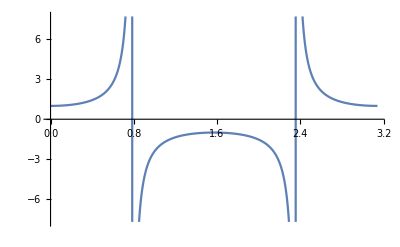

```mathematica
Plot[Sec[2θ],{θ,0,Pi}]
```

```mathematica
JacobianMatrix[S,CdS]//MatrixForm
```

(Sin[2 θ]/(2 √t) | 2 √t Cos[2 θ]
(√Cos[2 θ])/(4 t^(3/4)) | -(t^(1/4) Sin[2 θ])/(√Cos[2 θ]))

```mathematica
N[Integrate[1/Sqrt[-Cos[2θ]],{θ,Pi/4,3Pi/4}]]
```

2.62206+0. ⅈ

```mathematica
P={t^(1/2)*Sqrt[1-y^4],t^(1/4)*y}
```

{√t √(1-y^4),t^(1/4) y}

```mathematica
Ps={t,y}
```

{t,y}

```mathematica
JacobianMatrix[P,Ps]
```

{{(√(1-y^4))/(2 √t),-(2 √t y^3)/(√(1-y^4))},{y/(4 t^(3/4)),t^(1/4)}}

```mathematica
JacobianDeterminant[P,Ps]//Simplify
```

1/(2 t^(1/4) √(1-y^4))

```mathematica
Integrate[c*(2/a)*Sin[2*Pi*x/a]*x^2*Sin[2*Pi*m*x/a],{x,-a/2,a/2}]//Simplify
```

(a^2 c (-4 m (-1+m^2) π Cos[m π]-(-2-6 m^2+(-1+m^2)^2 π^2) Sin[m π]))/(2 (-1+m^2)^3 π^3)

```mathematica
Integrate[c*(2/a)*Sin[2Pi*x/a]^2*x^2,{x,-a/2,a/2}]
```

(a^2 c (-3+2 π^2))/(24 π^2)

```mathematica
(a^2 c (-4 m (-1+m^2) π Cos[m π]))/(2 (-1+m^2)^3 π^3)
```

-(2 a^2 c m Cos[m π])/((-1+m^2)^2 π^2)

```mathematica
Sum[-(2n)^2/((2n)^2 - 1)^3,{n,2,Infinity}]
```

(256-27 π^2)/1728

```mathematica
Integrate[((m*w)/(Pi*h))^(1/2)*c*x*E^(-(m*w*x^2)/h),{x,-Infinity,Infinity}]//Simplify
```

ConditionalExpression[0,Re[(m w)/h]≥0]

```mathematica
Integrate[(2/a)*Sin[Pi*x/a]^2,{x,0,a}]
```

1

```mathematica
Integrate[Sin[Pi*x/a]^2,{x,0,a}]
```

a/2

```mathematica
Integrate[(V/L)*Cos[2*Pi*x/L]*Cos[4*Pi*x/L],{x,0,L}]//Simplify
```

0

```mathematica
Integrate[Cos[2*Pi*x/L],{x,0,L}]
```

0

```mathematica
Integrate[Cos[2Pi*x/L],{x,0,L}]
```

0

```mathematica
H = (h/Sqrt[2]){{E1,LD},{LD,E2}}
```

{{(E1 h)/(√2),(h LD)/(√2)},{(h LD)/(√2),(E2 h)/(√2)}}

```mathematica
Eigenvalues[H]//Simplify
```

{(h (E1+E2-√(E1^2-2 E1 E2+E2^2+4 LD^2)))/(2 √2),(h (E1+E2+√(E1^2-2 E1 E2+E2^2+4 LD^2)))/(2 √2)}

```mathematica
Eigenvectors[H]//InputForm
```

{{-(-E1 + E2 + Sqrt[E1^2 - 2*E1*E2 + E2^2 + 4*LD^2])/(2*LD), 1}, 
 {-(-E1 + E2 - Sqrt[E1^2 - 2*E1*E2 + E2^2 + 4*LD^2])/(2*LD), 1}}

```mathematica
1/Norm[{-(-E1+E2+Sqrt[E1^2-2*E1*E2+E2^2+4*LD^2])/(2*LD),1}]//Simplify
```

2/(√(4+Abs[(-E1+E2+√(E1^2-2 E1 E2+E2^2+4 LD^2))/LD]^2))

```mathematica
1/Norm[{-(-E1+E2+Sqrt[E1^2-2*E1*E2+E2^2+4*LD^2])/(2*LD),1}]*{-(-E1+E2+Sqrt[E1^2-2*E1*E2+E2^2+4*LD^2])/(2*LD),1}//Simplify
```

{(E1-E2-√(E1^2-2 E1 E2+E2^2+4 LD^2))/(LD √(4+Abs[(-E1+E2+√(E1^2-2 E1 E2+E2^2+4 LD^2))/LD]^2)),2/(√(4+Abs[(-E1+E2+√(E1^2-2 E1 E2+E2^2+4 LD^2))/LD]^2))}

```mathematica
1/Norm[{-(-E1 + E2 - Sqrt[E1^2 - 2*E1*E2 + E2^2 + 4*LD^2])/(2*LD), 1}]
```

1/(√(1+1/4 Abs[(E1-E2+√(E1^2-2 E1 E2+E2^2+4 LD^2))/LD]^2))

```mathematica
Eigenvalues[{{0,1},{1,0}}]
```

{-1,1}

```mathematica
Eigenvectors[{{0,1},{1,0}}]
```

{{-1,1},{1,1}}

```mathematica
D[E^(-m*r)/r,r]//Simplify//InputForm
```

-((1 + m*r)/(E^(m*r)*r^2))

```mathematica
D[Sqrt[-t^2 + y^2 + z^2 + z^2],y]
```

y/(√(-t^2+y^2+2 z^2))

```mathematica
D[((1 + m*r)/(E^(m*r)*r^3)),r]//Simplify//TeXForm
```

-\frac{e^{-m r} \left(m^2 r^2+3 m r+3\right)}{r^4}

```mathematica
Sh = {r*Sin[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ],r*Cos[θ]}
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

```mathematica
Cd={r,θ,ϕ}
```

{r,θ,ϕ}

```mathematica
JacobianMatrix[Sh,Cd]
```

{{Cos[ϕ] Sin[θ],r Cos[θ] Cos[ϕ],-r Sin[θ] Sin[ϕ]},{Sin[θ] Sin[ϕ],r Cos[θ] Sin[ϕ],r Cos[ϕ] Sin[θ]},{Cos[θ],-r Sin[θ],0}}

```mathematica
JacobianMatrix[Sh,Cd]//MatrixForm
```

(Cos[ϕ] Sin[θ] | r Cos[θ] Cos[ϕ] | -r Sin[θ] Sin[ϕ]
Sin[θ] Sin[ϕ] | r Cos[θ] Sin[ϕ] | r Cos[ϕ] Sin[θ]
Cos[θ] | -r Sin[θ] | 0)

```mathematica
JacobianDeterminant[Sh,Cd]//Simplify
```

r^2 Sin[θ]

```mathematica
Transpose[JacobianMatrix[Sh,Cd]].JacobianMatrix[Sh,Cd]//Simplify//MatrixForm
```

(1 | 0 | 0
0 | r^2 | 0
0 | 0 | r^2 Sin[θ]^2)

```mathematica
Det[Transpose[JacobianMatrix[Sh,Cd]].JacobianMatrix[Sh,Cd]]//Simplify
```

r^4 Sin[θ]^2

```mathematica
Ex1={t^(1/4)*x,t^(1/6)*(1-x^4)^(1/6)}
```

{t^(1/4) x,t^(1/6) (1-x^4)^(1/6)}

```mathematica
CdX1={t,x}
```

{t,x}

```mathematica
(t^(1/4)*x)^4+(t^(1/6)*((1-x^4)^(1/6)))^6//Simplify
```

t

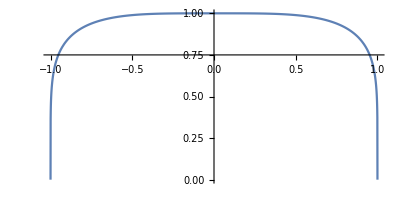

```mathematica
Show[ParametricPlot[{x,(1-x^4)^(1/6)},{x,-1,1}],PlotRange->All]
```

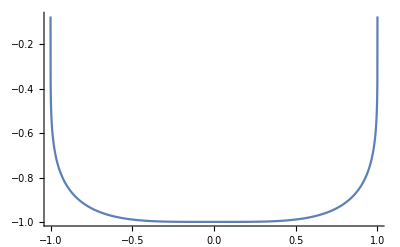

```mathematica
Plot[-(1-x^4)^(1/6),{x,-1,1},PlotRange->All]
```

```mathematica
JacobianMatrix[Ex1,CdX1]//MatrixForm
```

(x/(4 t^(3/4)) | t^(1/4)
((1-x^4)^(1/6))/(6 t^(5/6)) | -(2 t^(1/6) x^3)/(3 (1-x^4)^(5/6)))

```mathematica
Det[JacobianMatrix[Ex1,CdX1]]//Simplify
```

-1/(6 t^(7/12) (1-x^4)^(5/6))

```mathematica
Integrate[1/((1-x^4)^(5/6)),{x,-1,1}]
```

(3 Gamma[1/4] Gamma[7/6])/Gamma[5/12]

```mathematica
(t^(1/n)*x)^n + (t^(1/m)*(1-x^n)^(1/m))^m//Simplify
```

(t^(1/n) x)^n+(t^(1/m) (1-x^n)^(1/m))^m

```mathematica
Ex2={t^(1/n)*x,t^(1/m)*(1-x^n)^(1/m)}
```

{t^(1/n) x,t^(1/m) (1-x^n)^(1/m)}

```mathematica
Transpose[JacobianMatrix[Ex2,CdX1]].JacobianMatrix[Ex2,CdX1]//Simplify//MatrixForm
```

(((t^(2/n) x^2)/n^2+(t^(2/m) (1-x^n)^(2/m))/m^2)/t^2 | (t^(-1+2/n) x)/n-(n t^(-1+2/m) x^(-1+n) (1-x^n)^(-1+2/m))/m^2
(t^(-1+2/n) x)/n-(n t^(-1+2/m) x^(-1+n) (1-x^n)^(-1+2/m))/m^2 | t^(2/n)+(n^2 t^(2/m) x^(-2+2 n) (1-x^n)^(-2+2/m))/m^2)

```mathematica
Sqrt[Det[Transpose[JacobianMatrix[Ex2,CdX1]].JacobianMatrix[Ex2,CdX1]]]//Simplify//TeXForm
```

\sqrt{\frac{t^{2 \left(\frac{1}{m}+\frac{1}{n}-1\right)}
   \left(1-x^n\right)^{\frac{2}{m}-2}}{m^2}}

```mathematica
Integrate[(1-x^(2n))^(-1+1/(2m)),{x,-1,1},Assumptions->{Element[n,Integers],Element[m,Integers]} ]//TeXForm
```

\text{ConditionalExpression}\left[\, _2F_1\left(1-\frac{1}{2 m},\frac{1}{2 n};1+\frac{1}{2
   n};(-1)^{2 n}\right)+\frac{\Gamma \left(\frac{1}{2 m}\right) \Gamma \left(1+\frac{1}{2
   n}\right)}{\Gamma \left(\frac{m+n}{2 m n}\right)},n>0\land m>0\right]

```mathematica
Res[s3_]:=1-s3^k3
```

```mathematica
s1^k1 +((Res[s3] - s1^k1)^(1/k2))^k2//Simplify
```

s1^k1+((1-s1^k1-s3^k3)^(1/k2))^k2

```mathematica
Ex2={t^(1/k1)*s1,t^(1/k2)*(Res[s3]-s1^k1)^(1/k2)}
```

{s1 t^(1/k1),(1-s1^k1-s3^k3)^(1/k2) t^(1/k2)}

```mathematica
CdX2={t,s1}
```

{t,s1}

```mathematica
Sqrt[Det[Transpose[JacobianMatrix[Ex2,CdX2]].JacobianMatrix[Ex2,CdX2]]]//Simplify//TeXForm
```

\sqrt{\frac{\left(\text{s3}^{\text{k3}}-1\right)^2 t^{2
   \left(\frac{1}{\text{k1}}+\frac{1}{\text{k2}}-1\right)}
   \left(-\text{s1}^{\text{k1}}-\text{s3}^{\text{k3}}+1\right)^{\frac{2}{\text{k2}}-2}}{\text{k2}
   ^2}}

This is the ds1ds2 integral, the original integral is actually scaled down... more details in the TEX file. But in any case, the leftover factor is given in the next integral

```mathematica
Integrate[(1-s1^k1)^(-1+1/k2),{s1,-1,1},Assumptions->{Element[k1,Integers]@@Mod[k1,2]==0,Element[k2,Integers]@@Mod[k2,2]==0} ]
```

ConditionalExpression[(Gamma[1+1/k1] Gamma[1/k2])/Gamma[1/k1+1/k2]+Hypergeometric2F1[1/k1,(-1+k2)/k2,1+1/k1,(-1)^k1],Re[k2]>0&&Re[k1]>0]

This integral contains the scaling factor brought down from the previous integral. There’s also another factor of Res[s3] because it was the leading constant of the previous integral.

```mathematica
Integrate[Res[s3]^(1/(k1)+1/(k2)),{s3,-1,1},Assumptions->{Element[k1,Integers],Element[k2,Integers],R<1}]
```

ConditionalExpression[(Gamma[1+1/k1+1/k2] Gamma[1+1/k3])/Gamma[1+1/k1+1/k2+1/k3]+Hypergeometric2F1[-(k1+k2)/(k1 k2),1/k3,1+1/k3,(-1)^k3],k1 k2 (k1+k2+k1 k2)>0&&Re[k3]>0]

Testing if everything makes sense for a sphere of radius 1. This is the s1s2 integral.

```mathematica
Integrate[(1-s1^2)^(-1+1/2),{s1,-1,1} ]
```

π

This is the s3 integral. We see that the two integrals multiply to give (4/3)Pi

```mathematica
Integrate[(1-s3^2)^(1/2+1/2),{s3,-1,1}]
```

4/3

```mathematica
Integrate[(1-s1^k3)^(-1+1/k1+1/k2),{s1,-1,1},Assumptions->{Element[k1,Integers]@@Mod[k1,2]==0,Element[k2,Integers]@@Mod[k2,2]==0,Element[k3,Integers]@@Mod[k3,2]==0} ]
```

ConditionalExpression[(Gamma[1/k1+1/k2] Gamma[1+1/k3])/Gamma[1/k1+1/k2+1/k3]+Hypergeometric2F1[1-(k1+k2)/(k1 k2),1/k3,1+1/k3,(-1)^k3],Re[k3]>0&&Re[1/k1+1/k2]>0]

```mathematica
Integrate[(1-s4^(1/k4))^(-1+1/(k1)+1/(k2)+1/(k3)),{s4,-1,1},Assumptions->{Element[k1,Integers],Element[k2,Integers],Element[k3,Integers], Element[k4,Integers]}]
```

ConditionalExpression[(Gamma[1/k1+1/k2+1/k3] Gamma[1+k4])/Gamma[1/k1+1/k2+1/k3+k4]+Hypergeometric2F1[1-1/k1-1/k2-1/k3,k4,1+k4,(-1)^(1/k4)],k1 k2 k3 (k2 k3+k1 (k2+k3))>0&&k4>0]

```mathematica
Integrate[(1-s1^2)^(-1+1/2+1/2),{s1,-1,1}]
```

2

```mathematica
Integrate[(1-s4^2)^(-1+1/(2)+1/(2)+1/(2)),{s4,-1,1}]
```

π/2

```mathematica
DDD={(1-s2^k2-s3^k3)^(1/k1),s2,s3}
```

{(1-s2^k2-s3^k3)^(1/k1),s2,s3}

```mathematica
CDD = {s2,s3}
```

{s2,s3}

```mathematica
JacobianMatrix[DDD,CDD]//MatrixForm
```

JacobianMatrix[{(1-s2^k2-s3^k3)^(1/k1),s2,s3},{s2,s3}]